meta GGA kinetic energy functional
Perdew & Constantin, Phys. Rev. B 75, 155109 (2007)

```mathematica
(* 4-th order gradient exchange enhancement factor *)
Δ=8/81 q^2-1/9 p q +8/243 p^2
fGE4=1+5/27 p+20/9 q+Δ
DensityPlot[fGE4,{p,0,10},{q,0,10},
Axes-> True, AxesLabel->{"p","q"}]
(* modified 4-th order gradient expansion enhancement factor *)
fGE4M=fGE4/(√(1+(Δ/(1+5/3 p))^2))
DensityPlot[fGE4M,{p,0,10},{q,0,10},
Axes-> True, AxesLabel->{"p","q"}]
(* von-Weizsäcker enhancement factor *)
fW=5/3 p^2
DensityPlot[fW,{p,0,10},{q,0,10},
Axes-> True, AxesLabel->{"p","q"}]
```

(8 p^2)/243-(p q)/9+(8 q^2)/81

1+(5 p)/27+(8 p^2)/243+(20 q)/9-(p q)/9+(8 q^2)/81

-Graphics-

(1+(5 p)/27+(8 p^2)/243+(20 q)/9-(p q)/9+(8 q^2)/81)/(√(1+(((8 p^2)/243-(p q)/9+(8 q^2)/81)^2)/(1+(5 p)/3)^2))

-Graphics-

(5 p^2)/3

-Graphics-

0.5389

3

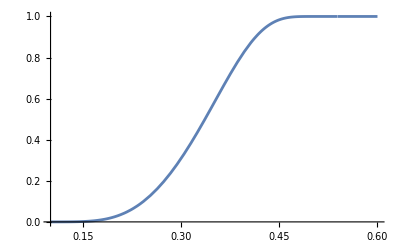

```mathematica
(* Switching function of Eqn. (15)*)
a=0.5389
b=3
fswitch[z_]:=Piecewise[{{0,z<=0},{((1+Exp[a/(a-z)])/(Exp[a/z]+Exp[a/(a-z)]))^b,0<=z<=a},{1,a<=z}}]
Plot[fswitch[z],{z,0.1, 0.6}]
```

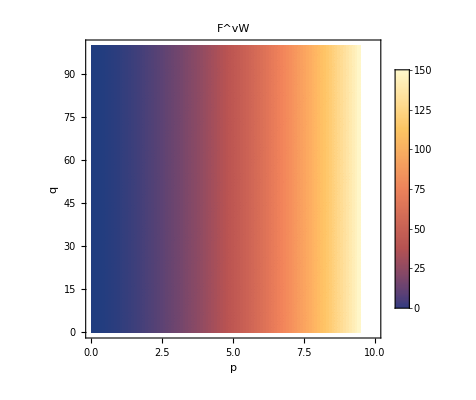
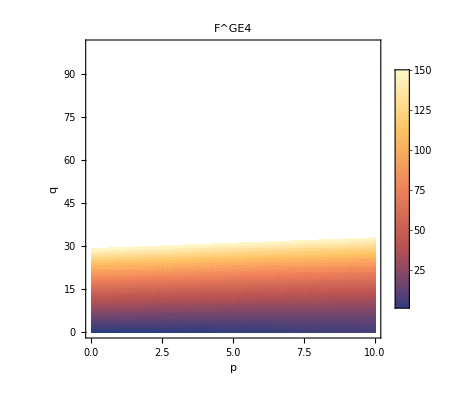
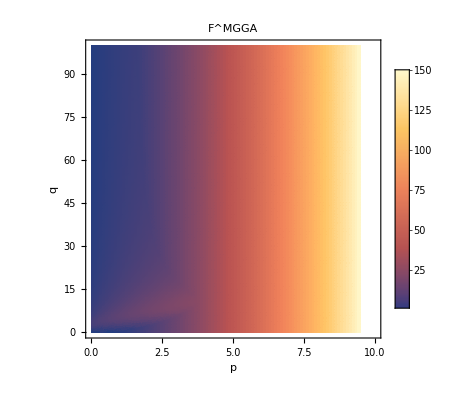
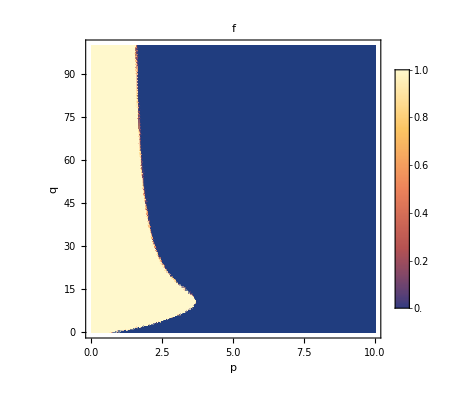

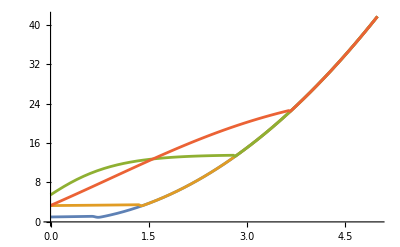

```mathematica
Δ=8/81 q^2-1/9 p q +8/243 p^2;
fGE4=1+5/27 p+20/9 q+Δ;
fGE4M=fGE4/(√(1+(Δ/(1+5/3 p))^2));
fW=5/3 p^2;
a=0.5389;
b=3;
fswitch[z_]:=Piecewise[{{0,z<=0},{((1+Exp[a/(a-z)])/(Exp[a/z]+Exp[a/(a-z)]))^b,0<z<a},{1,a<=z}}];
fMGGA=fW+(fGE4M-fW)*fswitch[fGE4M-fW];
{
DensityPlot[fW,{p,0,10},{q,0,100},
Axes-> True, AxesLabel->{"p","q"}, PlotPoints->100, PlotLegends-> Automatic, Exclusions-> None,PlotLabel->"F^vW",PlotRange->{0,150}],
DensityPlot[fGE4,{p,0,10},{q,0,100},
Axes-> True, AxesLabel->{"p","q"}, PlotPoints->100, PlotLegends-> Automatic, Exclusions-> None,PlotLabel->"F^GE4",PlotRange->{0,150}],
DensityPlot[fMGGA,{p,0,10},{q,0,100},
Axes-> True, AxesLabel->{"p","q"}, PlotPoints->100, PlotLegends-> Automatic, Exclusions-> None,PlotLabel->"F^MGGA",PlotRange->{0,150}],
DensityPlot[fswitch[fGE4M-fW],{p,0,10},{q,0,100},
Axes-> True, AxesLabel->{"p","q"}, PlotPoints->100, PlotLegends-> Automatic, Exclusions-> None,PlotLabel->"f"]

}
Plot[{fMGGA/.{q->0.0},fMGGA/.{q->1.0},fMGGA/.{q->5.0},fMGGA/.{q->10.0}},{p,0,5}]
```